```mathematica
M4[s_,t_]:= 1/(s-M^2)+1/(u-M^2)/.{u -> 4m^2-s-t};

Residue[M4[s,t]/((s-2m^2)^2(s-(2m^2-t))),{s,2m^2}]+Residue[M4[s,t]/((s-2m^2)^2(s-(2m^2-t))),{s,2m^2-t}]//FullSimplify
```

-(-4 m^2+2 M^2+t)/((-2 m^2+M^2)^2 (-2 m^2+M^2+t)^2)

```mathematica
Series[-(-4 m^2+2 M^2+t)/((-2 m^2+M^2)^2 (-2 m^2+M^2+t)^2),{t,0,2}]
```

2/((2 m^2-M^2)^3)+(3 t)/((2 m^2-M^2)^4)+(4 t^2)/((2 m^2-M^2)^5)+O[t]^3

```mathematica
K[s_,t_]:=1/((s-2m^2)^2(s-(2m^2-t)));

SeriesCoefficient[(K[M^2,t]-K[4m^2-M^2-t,t])*LegendreP[J,1+(2*t)/(M^2-4m^2)],{t,0,0}]

SeriesCoefficient[(K[M^2,t]-K[4m^2-M^2-t,t])*LegendreP[J,1+(2*t)/(M^2-4m^2)],{t,0,1}]

(* J=0 *)
Series[(K[M^2,t]-K[4m^2-M^2-t,t])*LegendreP[0,1+(2*t)/(M^2-4m^2)],{t,0,1}]
```

-2/((2 m^2-M^2)^3)

-3/((2 m^2-M^2)^4)-(2 J (1+J))/((2 m^2-M^2)^3 (-4 m^2+M^2))

-2/((2 m^2-M^2)^3)-(3 t)/((2 m^2-M^2)^4)+O[t]^2

(3 M^2)/(4 m^2-2 M^2)

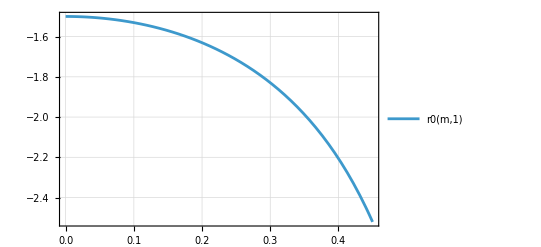

```mathematica
r0[m_,M_]:=(-3/((M^2-2m^2)^4))/(-2/((2m^2-M^2)^3))*M^2

r0[m,M]//FullSimplify

Plot[r0[m,1],{m,0.00,0.45},PlotTheme->"Detailed"]
```

```mathematica
Solve[1/(s-M^2)*a-1/(s-M^2)*LegendreP[0,1+(2t)/(s-4m^2)]==0,{a}]
```

{{a→1}}

```mathematica
M42[s_, t_] := 1/M^4*(((t - u)^2 - (4 m^2 - s)^2/3)/(s-M^2)+((t - s)^2 - (4 m^2 - u)^2/3)/(u-M^2))/.{u -> 4m^2-s-t}
```

```mathematica
b = Residue[M42[s,t]/((s-2m^2)^2(s-(2m^2-t))),{s,2m^2}]+Residue[M42[s,t]/((s-2m^2)^2(s-(2m^2-t))),{s,2m^2-t}]//FullSimplify
```

-(2 (-4 m^2+2 M^2+t) ((-4 m^2+M^2)^2+6 (-4 m^2+M^2) t+6 t^2))/(3 M^4 (-2 m^2+M^2)^2 (-2 m^2+M^2+t)^2)

```mathematica
SeriesCoefficient[b,{t,0,0}]//FullSimplify

SeriesCoefficient[b,{t,0,1}]//FullSimplify
```

-(4 (-4 m^2+M^2)^2)/(3 M^4 (-2 m^2+M^2)^3)

(-32 m^4+32 m^2 M^2-6 M^4)/((-2 m^2 M+M^3)^4)

```mathematica
(* J=2 *)
Series[(K[M^2,t]-K[4m^2-M^2-t,t])*LegendreP[2,1+(2*t)/(M^2-4m^2)],{t,0,1}]
((3 (4 m^2-3 M^2))/((2 m^2-M^2)^4 (4 m^2-M^2)))/(-2/((2 m^2-M^2)^3))//FullSimplify

((-32 m^4+32 m^2 M^2-6 M^4)/((-2 m^2 M+M^3)^4))/(-(4 (-4 m^2+M^2)^2)/(3 M^4 (-2 m^2+M^2)^3))//FullSimplify
```

-2/((2 m^2-M^2)^3)+(3 (4 m^2-3 M^2) t)/((2 m^2-M^2)^4 (4 m^2-M^2))+O[t]^2

-(3 (4 m^2-3 M^2))/(2 (8 m^4-6 m^2 M^2+M^4))

-(3 (4 m^2-3 M^2))/(2 (8 m^4-6 m^2 M^2+M^4))

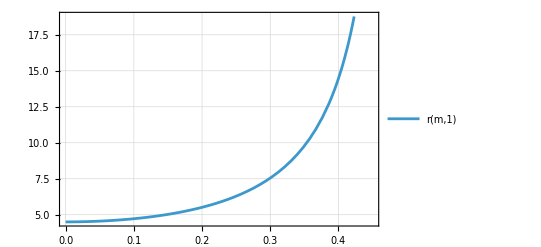

g3[0.4,  1]/g2[0.4,  1]*M^2=14.4608

```mathematica
r[m_,M_]:=((3 (4 m^2-3 M^2))/((2 m^2-M^2)^4 (4 m^2-M^2)))/(-2/((2 m^2-M^2)^3));

Plot[r[m,1],{m,0.0,0.45},PlotTheme->"Detailed"]

Print["g3[0.4,  1]/g2[0.4,  1]*M^2=", r[0.40,1]];
```